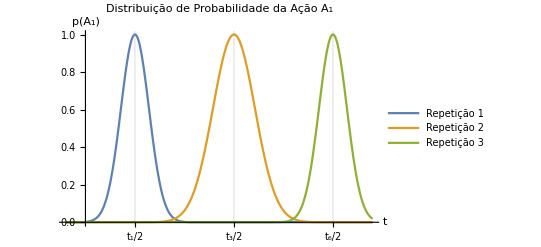

Export::nodir: Directory /Users/Rogiel/Images/ does not exist.

Export::noopen: Cannot open /Users/Rogiel/Images/Exemplo_BO_Media.pdf.

$Failed

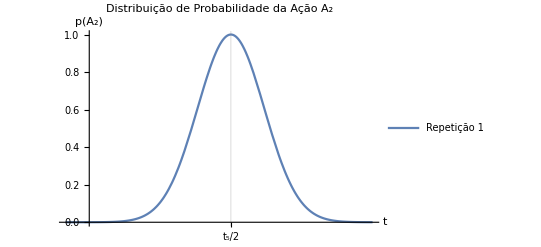

```mathematica
Plot[{
Exp[-(t-1)^2/Power[0.2, 2]],
Exp[-(t-2)^2/Power[0.3, 2]],
Exp[-(t-3)^2/Power[0.2, 2]]
},{t,0.3,3.4},
Ticks->{{
{1, "t_1/2"},
{2, "t_3/2"},
{3, "t_6/2"}
}, {}},
GridLines->{{
1,2, 3
}, {}},
PlotRange->Full,
PlotLegends->{"Repetição 1", "Repetição 2", "Repetição 3"},
AxesLabel->{"t", "p(A_1)"},
PlotLabel->"Distribuição de Probabilidade da Ação A_1"
]
Export[NotebookDirectory[]<>"Images/Exemplo_BO_Media_A1.pdf", %];

Plot[{
Exp[-(t-1)^2/Power[0.2, 2]]
},{t,0.3,1.6},
Ticks->{{
{1, "t_5/2"}
}, {}},
GridLines->{{
1
}, {}},
PlotRange->Full,
PlotLegends->{"Repetição 1", "Repetição 2", "Repetição 3"},
AxesLabel->{"t", "p(A_2)"},
PlotLabel->"Distribuição de Probabilidade da Ação A_2"
]
Export[NotebookDirectory[]<>"Images/Exemplo_BO_Media_A2.pdf", %]
```